```mathematica
rsize[n_,m_] := If[m<n, Sum[Binomial[m-1,i],{i,0,n}],1+Sum[Binomial[m-1,i],{i,0,n-1}]]
csize[n_,m_]:= If[m<n, Sum[Binomial[m,i],{i,0,n}],1+Sum[Binomial[m,i],{i,0,n-1}]]
```

```mathematica
{rsize[2,12],csize[2,12]}
```

{13,14}

```mathematica
nboson = 3;
lsize = 100;
```

```mathematica
rlst = Table[{i,rsize[nboson,i]},{i,1,lsize-1}];
clst = Table[{i,csize[nboson,i]},{i,1,lsize-1}];
```

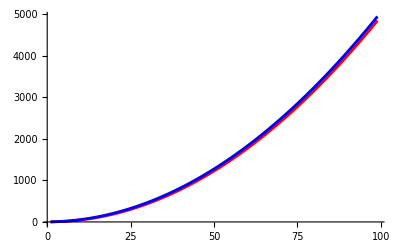

```mathematica
Show[ListPlot[rlst,PlotStyle->Red,Joined->True],ListPlot[clst,PlotStyle->Blue,Joined->True],PlotRange->All]
```